```mathematica
ClearAll["Global`*"]
```

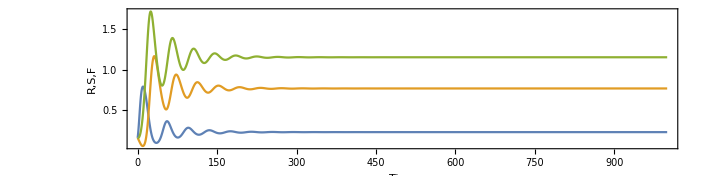

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,m_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(ρ*X[t] + m*Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==0.16,X[0]==0.16,Y[0]==0.16},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,σ=0.3,ρ=0.2,m=0.2,μ=0.3,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,m,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == ts*(α*R*(1-R)-R*(ρ*H+m*F)),
0==ts*(σ*(1-R)*F-ρ*R*H-μ*H), 
0==ts*(λ*F-σ*(1-R)*F+ρ*R*H)},
{R,H,F}]]
```

{{R→0,H→0,F→0},{R→1,H→0,F→0},{R→(μ (-λ+σ))/(λ ρ+μ σ),H→(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ)),F→(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))}}

```mathematica
InternalSol1 = Sol[[3]];
(*InternalSol2 = Sol[[4]];*)
```

```mathematica
{InternalSol1}/.{α->0.5,λ->0.1,μ->0.2,ρ->0.5,σ->0.5, m->0.2}
```

{{R→0.533333,H→0.259259,F→0.518519}}

This means only InternalSol2 is an INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

```mathematica
Rstar = IntPosSol[[1]][[2]]
Hstar = IntPosSol[[2]][[2]]
Fstar = IntPosSol[[3]][[2]]
```

(μ (-λ+σ))/(λ ρ+μ σ)

(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))

(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))

```mathematica
Limit[Rstar,σ->0]
Limit[Fstar,σ->0]
```

-μ/ρ

(α μ (μ+ρ))/(ρ (m μ+λ ρ))

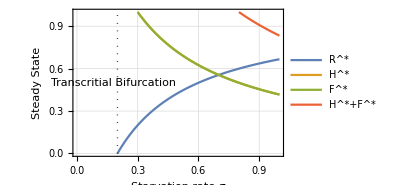

```mathematica
With[{alpha=0.5,lambda=0.2,mu=0.2,rho=0.2,mr=0.2},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho,m->mr};
FigFP=
Show[{
Plot[{Rstarspec,Xstarspec,Ystarspec,Xstarspec+Ystarspec},{σ,lambda,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","Steady State"},PlotRange->{{0,1},{0,1}},ImageSize->300,PlotLegends->{"R^*","H^*","F^*","H^*+F^*"}],
Graphics[{Dotted,Line[{{lambda,0},{lambda,1}}]}],
Graphics[Rotate[Text["Transcritial Bifurcation",{(lambda-0.02),0.5}],90Degree]]
}]
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf",FigFP]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf

```mathematica
Limit[{Rstarspec,Xstarspec,Ystarspec},σ->Infinity]
```

{1.,0.,0.}

```mathematica
dF =λ*F-σ*(1-R)*F+ρ*R*H;
dH =σ*(1-R)*F-ρ*R*H-μ*H;
dR=   α*R*(1-R)-R*(ρ*H+m*F);
JacSpec = {
{D[dF,F],D[dF,H],D[dF,R]},
{D[dH,F],D[dH,H],D[dH,R]},
{D[dR,F],D[dR,H],D[dR,R]}
}
```

{{λ-(1-R) σ,R ρ,H ρ+F σ},{(1-R) σ,-μ-R ρ,-H ρ-F σ},{-m R,-R ρ,-F m+(1-R) α-R α-H ρ}}

```mathematica
JacSpec//MatrixForm
```

(λ-(1-R) σ | R ρ | H ρ+F σ
(1-R) σ | -μ-R ρ | -H ρ-F σ
-m R | -R ρ | -F m+(1-R) α-R α-H ρ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,H->Hstar,F->Fstar};
JacSpecSolTriv = JacSpe/.{R->0,H->0,F->0}
```

JacSpe

```mathematica
JacSpecSol
```

{{λ-σ (1-(μ (-λ+σ))/(λ ρ+μ σ)),(μ ρ (-λ+σ))/(λ ρ+μ σ),(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))+(α λ μ (μ+ρ) σ)/((m μ+λ ρ) (λ ρ+μ σ))},{σ (1-(μ (-λ+σ))/(λ ρ+μ σ)),-μ-(μ ρ (-λ+σ))/(λ ρ+μ σ),-(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α λ μ (μ+ρ) σ)/((m μ+λ ρ) (λ ρ+μ σ))},{-(m μ (-λ+σ))/(λ ρ+μ σ),-(μ ρ (-λ+σ))/(λ ρ+μ σ),-(m α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α λ^2 ρ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))-(α μ (-λ+σ))/(λ ρ+μ σ)+α (1-(μ (-λ+σ))/(λ ρ+μ σ))}}

```mathematica
FullSimplify[JacSpecSol]//MatrixForm
```

((λ ρ (λ-σ))/(λ ρ+μ σ) | (μ ρ (-λ+σ))/(λ ρ+μ σ) | (α λ (μ+ρ))/(m μ+λ ρ)
(λ (μ+ρ) σ)/(λ ρ+μ σ) | -(μ (μ+ρ) σ)/(λ ρ+μ σ) | -(α λ (μ+ρ))/(m μ+λ ρ)
(m μ (λ-σ))/(λ ρ+μ σ) | (μ ρ (λ-σ))/(λ ρ+μ σ) | (α μ (λ-σ))/(λ ρ+μ σ))

```mathematica
({R,H,F}/.Sol)/.{α->alpha,λ->lambda,μ->mu,ρ->rho,σ->sigma,m->mr}
```

{{0,0,0},{1,0,0},{(mu (-lambda+sigma))/(lambda rho+mu sigma),(alpha lambda^2 (mu+rho))/((mr mu+lambda rho) (lambda rho+mu sigma)),(alpha lambda mu (mu+rho))/((mr mu+lambda rho) (lambda rho+mu sigma))}}

This plot shows that the bifurcation at lambda=sigma is a Transcritical (I think)

```mathematica
({R,H,F}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma}
```

{{0,0,0},{1,0,0},{(0.2 (-0.1+sigma))/(0.02+0.2 sigma),0.0333333/(0.02+0.2 sigma),0.0666667/(0.02+0.2 sigma)}}

```mathematica
Manipulate[
Eig = Eigenvalues[JacSpecSol/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma}];
REig = Re[Eig];
IEig = Im[Eig];
MaxEig = Round[Max[REig],0.000001];
{ListPlot[{{0,0},{0, (μ (-λ+σ))/(λ ρ+μ σ)}}/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma},PlotStyle->Large,PlotRange->{{-1,1},{-1,1}}],
Show[{
ListPlot[Transpose[{REig,IEig}],PlotRange->{{-1,1},{-1,1}}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"},PlotLabel->MaxEig]},
{{sigma,0.5},0,1,0.001}]
```

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]],Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]],Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]],Im[Eigenvalues[JacSpecSol]]}],PlotRange→{{-1,1},{-1,1}}],},ImageSize→300,Frame→True,AspectRatio→1,FrameLabel→{Real part,Imaginary part},PlotLabel→Round[Re[Eigenvalues[JacSpecSol]],1.×10^-6]].

The internal fixed point crosses ‘0’ and exchanges stability. This is a classic TransCritical bifurcation!

```mathematica
Eig
```

{-0.348962+0. ⅈ,0.00738149+0.151722 ⅈ,0.00738149-0.151722 ⅈ}

```mathematica
Manipulate[
Eig = Eigenvalues[JacSpecSol/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma}];
REig = Re[Eig];
IEig = Im[Eig];
Row[{
Show[{
ListPlot[Transpose[{REig,IEig}],PlotRange->{{-1,1},{-1,1}}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"}],
FP=({R,H,F}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma};
Show[{
ListPointPlot3D[FP,
PlotStyle->Directive[{ColorData[97,4],PointSize[Large]}],PlotLabel->FP,PlotRange->{{-1,1},{0,1},{0,1}},ImageSize->300,AxesLabel->{"R^*","S^*","F^*"}],
Graphics3D[{Opacity[0.5],Polygon[{{0,0,0},{0,1,0},{0,1,1},{0,0,1}}]}]
}]
}],
{{sigma,0.1},0,1,0.001}]
```

```mathematica
FP
```

{{0,0,0},{1,0,0},{0.,0.166667,0.333333}}

Specific Bifurcations

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,μ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,α]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,ρ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,λ]
```

{{σ→λ}}

{{μ→0},{μ→-ρ}}

{{α→0}}

{{ρ→-μ}}

{{λ→0},{λ→σ}}

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,muy];
```

$Aborted

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfAnalytic = Solve[Det[Sylv]==0,ρ];
```

```mathematica
HopfAnalytic
```

1
 |  |  |  |

```mathematica
FullSimplify[HopfAnalytic]
```

$Aborted

The solution to the Hopf Bifurcation surface may not be analytically tractable
Try Solving numerically with a = 1

```mathematica
Hsp = HopfAnalytic/.{α->0.5,μ->0.1,m->MR,λ->0.2}; (*{α->0.5,μ->0.2,m->MR,λ->0.2}*)
curves = Table[ρ/.Hsp[[4]],{MR,0.1,1,0.1}];
```

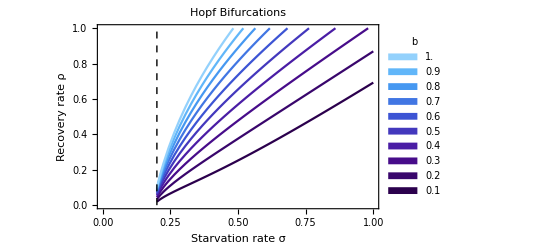

```mathematica
HopfPlot = Show[{
Plot[curves,{σ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->ColorData["DeepSeaColors"]/@(Range[0,Length@curves]/Length@curves),PlotLegends->SwatchLegend[ Table[MR,{MR,0.1,1,0.1}],LegendLayout->{"ReversedColumn",1},LegendLabel->Style["b",Italic]],PlotLabel->"Hopf Bifurcations",
RegionFunction->Function[{x,y},x>0.2]],
Graphics[{Dashed,Line[{{0.2,0},{0.2,1}}]}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_HopfPlotb.pdf",HopfPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_HopfPlotb.pdf

```mathematica
ColorData[35,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Hsp
```

{{λ→σ},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,1]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,2]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,3]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,4]},{λ→Root[0.000576 σ^2+(-0.00032 σ+0.00432 σ^2) #1+(-0.00576 σ+0.0088 σ^2) #1^2+(0.00016-0.024 σ+0.008 σ^2) #1^3+(0.0024-0.016 σ) #1^4+0.008 #1^5&,5]}}

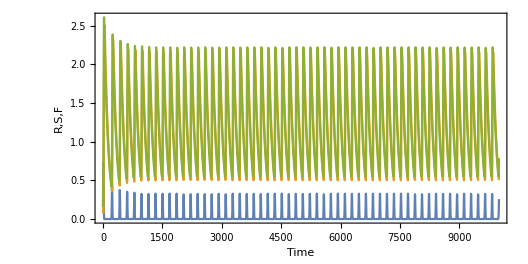

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,m_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(ρ*X[t] + m*Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==0.16,X[0]==0.16,Y[0]==0.16},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,σ=0.21,ρ=0.2,m=0.2,μ=0.2,T=10000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,m,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.5,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

```mathematica
Show[{
ParallelTable[
Hsp2 =HopfAnalytic/.{λ->0.2,μ->0.1,m->MR};
Plot3D[ρ/.Hsp2[[4]],{σ,0.2,1},{α,0,2},PlotRange->{0,1}, 
ClippingStyle->None,PlotStyle->{Directive[ColorData[97,1],Opacity[0.8]],Directive[ColorData[97,1],Opacity[0.8]]},Mesh->5,AxesLabel->{"σ","α","ρ"},Lighting->{{"Ambient", White}}],{MR,{0.2,1}}] (*RegionFunction->Function[{x,y,z},x>y],*)
}]
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -0.0666667 + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
Hsp3 = HopfAnalytic/.{α->0.5,μ->0.2,λ->0.1};
Plot3D[ρ/.Hsp3[[4]],{σ,0,1},{m,0,2}]
```

-Graphics3D-

```mathematica
HopfData = Table[{σ,Re[N[λ/.Hsp[[4]]]]},{σ,0.1,1,0.01}];
(*HopfData=Join[{Reverse[HopfNumSol2down,2]/.σ->"NA",Reverse[HopfNumSol2up,2]/.σ->"NA"}];*)
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv",HopfData,"CSV"]
```

```mathematica
Hsp2LS = Hsp2[[4]]/.σ->λ;
```

Part::partd: Part specification Hsp2 ⟦ 4 ⟧ is longer than depth of object.

```mathematica
(*values = {α->0.5,μ->0.1,m->0.1,λ->0.2};*)
HopfValues =With[{ts=1,
(*B0*)B0=1.9*10^(-2),
(*Bm*)Bm=0.0245,
(*Em*)Em=21.39/2*1000(*J/gram*),
(*η*)η=3/4,
(*η2*)η2=-0.206,
(*λ0*)λ0=3.3879*10^(-7),
(*ef*)ef=0.001,
(*γ*)γ=1.19,
(*ζ*)ζ=1.01,
(*f0*)f0=0.0202,
(*mm0*)mm0=0.324,
M=10},

growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;
values =  {α->resourcegrowth,μ->mortality,m->maintenance,λ->growth};
FstarValue = Flatten[ParallelTable[{σ,ρ,N[(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))]},{σ,0.00001,0.01,0.00001},{ρ,0.00001,0.01,0.00001}]/.values,1];
HstarValue = Flatten[ParallelTable[{σ,ρ,N[(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))]},{σ,0.00001,0.01,0.00001},{ρ,0.00001,0.01,0.00001}]/.values,1];
RstarValue = Flatten[ParallelTable[{σ,ρ,N[(μ (-λ+σ))/(λ ρ+μ σ)]},{σ,0.00001,0.01,0.00001},{ρ,0.00001,0.01,0.00001}]/.values,1];
Table[Flatten[ {σ,Select[Re[ρ/.(HopfAnalytic/.values)],#>0&]},1],{σ,0.00001,0.01,0.00001}]

](*{α->0.5,μ->0.2,m->MR,λ->0.2}*);
```

```mathematica
HopfFixedPointPlot = Legended[
GraphicsRow[{
Show[{
ListDensityPlot[RstarValue,ColorFunction->ColorData["SouthwestColors"](*,ColorFunctionScaling->False*)(*,PlotLegends->Automatic*),
PlotLabel->"R Steady State",FrameLabel->{"Starvation Rate σ","Recovery Rate ρ"},PlotRange->{{0.0001,0.01},{0.0001,0.01},All}],
ListLinePlot[HopfValues,PlotStyle->Black],
Graphics[Text["Cycles",{0.35,0.9}]],
Graphics[Text["Fixed Points",{0.78,0.1}]],
Graphics[{Dashed,Line[{{0.2,0},{0.2,1}}]}],
Graphics[{White,Rotate[Text["Hopf",{0.4,0.25}],35Degree]}],
Graphics[{White,Text["TC",{0.25,0.55}]}]
(*ListPlot[Table[N[ρ/.Hsp],{σ,0.2,1,0.1}],PlotRange->{0,1},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->White,PlotLabel->"Hopf Bifurcations"]*)
}],
Show[{
ListDensityPlot[HstarValue,ColorFunction->ColorData["SouthwestColors"](*,ColorFunctionScaling->False*)(*,PlotLegends->Automatic*),
PlotLabel->"H Steady State",FrameLabel->{"Starvation Rate σ","Recovery Rate ρ"},PlotRange->{{0.0001,0.01},{0.0001,0.01},All}],
ListLinePlot[HopfValues,PlotStyle->Black],
Graphics[Text["Cycles",{0.35,0.9}]],
Graphics[Text["Fixed Points",{0.78,0.1}]],
Graphics[{Dashed,Line[{{0.2,0},{0.2,1}}]}],
Graphics[{White,Rotate[Text["Hopf",{0.4,0.25}],35Degree]}],
Graphics[{White,Text["TC",{0.25,0.55}]}]
(*ListPlot[Table[N[ρ/.Hsp],{σ,0.2,1,0.1}],PlotRange->{0,1},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->White,PlotLabel->"Hopf Bifurcations"]*)
}],
Show[{
ListDensityPlot[FstarValue,ColorFunction->ColorData["SouthwestColors"](*,ColorFunctionScaling->False*)(*,PlotLegends->Automatic*),
PlotLabel->"F Steady State",FrameLabel->{"Starvation Rate σ","Recovery Rate ρ"},PlotRange->{{0.0001,0.01},{0.0001,0.01},All}],
ListLinePlot[HopfValues,PlotStyle->Black],
Graphics[Text["Cycles",{0.35,0.9}]],
Graphics[Text["Fixed Points",{0.78,0.1}]],
Graphics[{Dashed,Line[{{0.2,0},{0.2,1}}]}],
Graphics[{White,Rotate[Text["Hopf",{0.85,0.65}],40Degree]}],
Graphics[{White,Text["TC",{0.25,0.55}]}]
(*ListPlot[Table[N[ρ/.Hsp],{σ,0.2,1,0.1}],PlotRange->{0,1},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->White,PlotLabel->"Hopf Bifurcations"]*)
}]
},ImageSize->600],
BarLegend[{"SouthwestColors",{0,1}},LegendLayout->"Column",LegendMarkerSize->200]
]
```

$Aborted

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_HopfFP.jpg",HopfFixedPointPlot,"JPEG",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_HopfFP.jpg

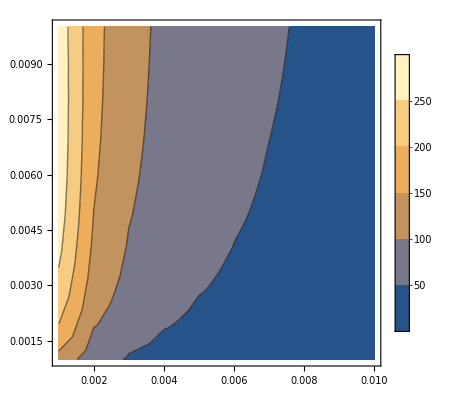

```mathematica
With[{ts=1,
(*B0*)B0=1.9*10^(-2),
(*Bm*)Bm=0.0245,
(*Em*)Em=21.39/2*1000(*J/gram*),
(*η*)η=3/4,
(*η2*)η2=-0.206,
(*λ0*)λ0=3.3879*10^(-7),
(*ef*)ef=0.001,
(*γ*)γ=1.19,
(*ζ*)ζ=1.01,
(*f0*)f0=0.0202,
(*mm0*)mm0=0.324,
M=10},

growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;
values =  {α->resourcegrowth,μ->mortality,m->maintenance,λ->growth};
FstarValue = Flatten[ParallelTable[{σ,ρ,N[(α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))]},{σ,0.001,0.01,0.001},{ρ,0.001,0.01,0.001}]/.values,1];
HstarValue = Flatten[ParallelTable[{σ,ρ,N[(α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ))]},{σ,0.001,0.01,0.001},{ρ,0.001,0.01,0.001}]/.values,1];
RstarValue = Flatten[ParallelTable[{σ,ρ,N[(μ (-λ+σ))/(λ ρ+μ σ)]},{σ,0.2,1,0.01},{ρ,0,1,0.01}]/.values,1];

ListContourPlot[FstarValue,PlotLegends->True,PlotRange->All]
]
```